## Combi - Example sheet x

Problem 1
a)

```mathematica
Clear[a]
Clear[b]
Clear[c]
a=0.1;
b=1;
c=0.5;
d=1;
dS[S_,P_,k_]:=b(S-P)-c S - (S(P+S))/k-a S P 
dP[S_,P_,k_]:=-c P - (P(P+S))/k+a S P
solution[k_]:=Solve[{dS[s,p,k]==0,dP[s,p,k]==0},{s,p}];
s[k_]:=s/.solution[k]
p[k_]:=p/.solution[k]
s[k]
p[k]
s0=s[30];
p0=p[30];
(*kc/.Solve[{p[kc]==0},kc][[1]]
a=1;
b=2;
c=1.5;
Kmin=b/(a(b-c))-10;
Kmax=b/(a(b-c))+10;
Show[Plot[s[K],{K,Kmin,Kmax}],Plot[p[K],{K,Kmin,Kmax}],PlotRange->All]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-6.28667,0.,7.95334,15.}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-27.5733,0.,0.906673,0.}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
b)
```

```mathematica
c=2.1;
StreamPlot[{v,-c v -u(1-u)},{u,-0.5,1.5},{v,-1,1}]
ParametricPlot[{v[t], -c v[t] - u[t](1-u[t])},{t,-0.5,1.5}]
```

```mathematica
c)
```

```mathematica
a=0.1;
b=1;
c=0.5;
k=30;
d=0;
L=100;
timeSteps=1000;
S=Table[0,{i,1,100},{j,1,timeSteps}];
P=Table[0,{i,1,100},{j,1,timeSteps}];
S[[50]][[1]]=15;
P[[50]][[1]]=0;
dt=0.01;

For[t=2,t≤timeSteps,t++,For[i=1,i≤L,i++,{S[[i]][[t]]=S[[i]][[t-1]]+(b(S[[i]][[t-1]]+P[[i]][[t-1]])-c S[[i]][[t-1]]-(S[[i]][[t-1]](P[[i]][[t-1]]+S[[i]][[t-1]]))/k-a S[[i]][[t-1]]P[[i]][[t-1]]+d(S[[Mod[(i+1)-1,L]+1]][[t-1]]-2 S[[i]][[t-1]] +S[[Mod[(i-1)-1,L]+1]][[t-1]]))dt,P[[i]][[t]]=P[[i]][[t-1]]+(-c P[[i]][[t-1]]-(P[[i]][[t-1]](P[[i]][[t-1]]+S[[i]][[t-1]]))/k+a S[[i]][[t-1]]P[[i]][[t]]+d(P[[Mod[(i+1)-1,L]+1]][[t-1]]-2 P[[i]][[t-1]] +P[[Mod[(i-1)-1,L]+1]][[t-1]]))dt}]]
```

```mathematica
Mod[(49+1)-1,L]+1
Mod[(49-1)-1,L]+1
```

```mathematica
s0
p0
```

7.95334

0.906673

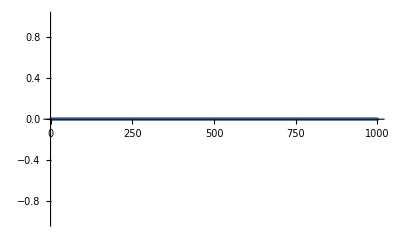

```mathematica
ListPlot[P[[50]],PlotRange->All]
```

```mathematica
t=2
```

```mathematica
S[[Mod[(i+1)-1,L]+1]][[t-1]]-2 S[[i]][[t-1]] +S[[Mod[(i-1)-1,L]+1]][[t-1]]
```

```mathematica
S[[49]]
```

```mathematica
S[[50]]
```

```mathematica
Mod[1-1-1,100]+1
```

Problem 2
a)
b)